```mathematica
ClearAll["Global`*"];
Remove["Global`*"];
```

```mathematica
results={};
sols={};
δvec=(Table[10^eδ,{eδ,-10,-2}]~Join~Table[δ,{δ,10^-1,9/10,1/10}]~Join~Table[δ,{δ,1,2,1/5}])//Reverse;
(*f0vec=Table[10^eδ,{eδ,-21,-1,5}]//Reverse;*)
f0vec={10^-15}//Reverse;
For[if0=1,if0≤Length[f0vec],if0+=1,
fixf0results={};
f0=f0vec[[if0]];
For[iδ=1,iδ≤Length[δvec],iδ+=1,
δ=δvec[[iδ]];
ϵ=10^-40;λ=Rationalize[638.5^2,0];k=Rationalize[1.2383 √λ,0];q=k(1-δ);
U[G_]:=G^2/12;a=1/(√6);
Ω[ϕ_,G_]:=k ((U[G]+1-a ϕ)-(1)E^(-a ϕ));
ς[ϕ_,G_]:=18((a Ω[ϕ,G]+D[Ω[ϕ,G], ϕ])^2+(D[Ω[ϕ,G], G])^2)-12 Ω[ϕ,G]^2-24k Ω[ϕ,G] (1)E^(-a ϕ);
dςdϕ[ϕ_,G_]:=12 a k^2 (2-(1)2 ⅇ^(-2 a ϕ)+(-2+3 a^2) (-U[G]+a ϕ));
dςdG[ϕ_,G_]:=-12 k^2 U'[G] (2+(-2+3 a^2) (-U[G]+a ϕ)-3 U''[G]);
eqn1=3(q z+1)(f'[z]β[z]+f[z](a ϕ'[z]β[z]+β'[z]))-12f[z] β[z]^2==ς[ϕ[z],G[z]]-(1)12 E^(-2a ϕ[z])k^2;
eqn2=6(a ϕ'[z]β[z]+β'[z])==(q z+1)((ϕ'[z])^2+(G'[z])^2);
eqn3=f[z](a(q z+1)(ϕ'[z])^2+(q-4β[z])ϕ'[z]+(q z+1)ϕ''[z])+(q z+1)f'[z]ϕ'[z]==1/(q z+1)(2a ς[ϕ[z],G[z]]+dςdϕ[ϕ[z],G[z]]);
eqn4=f[z](a(q z+1)ϕ'[z]G'[z]+(q-4β[z])G'[z]+(q z+1)G''[z])+(q z+1)f'[z]G'[z]==1/(q z+1)dςdG[ϕ[z],G[z]];
ic1=ϕ[ϵ]==D[√(8/3)λ(z+1/k)^2,{z,0}]/.z->ϵ;
ic2=ϕ'[ϵ]==D[√(8/3)λ(z+1/k)^2,{z,1}]/.z->ϵ;
ic3=G[ϵ]==D[√(24λ)(z+1/k),{z,0}]/.z->ϵ;
ic4=G'[ϵ]==D[√(24λ)(z+1/k),{z,1}]/.z->ϵ;
ic5=f[ϵ]==1;
ic6=β[ϵ]==Ω[ϕ[ϵ],G[ϵ]]+q E^(-a ϕ[ϵ]);
ϕExact[z_]:=√(8/3)λ(z+1/k)^2;
GExact[z_]:=√(24λ)(z+1/k);
fExact[z_]:=1;
βExact[z_]:=k ((U[GExact[z]]+1-a ϕExact[z])-E^(-a ϕExact[z]))+q E^(-a ϕExact[z]);
tmp=Reap[NDSolve[{eqn1,eqn2,eqn3,eqn4,ic1,ic2,ic3,ic4,ic5,ic6},{ϕ,G,f,β},{z,ϵ,100k},AccuracyGoal->∞,WorkingPrecision->100,MaxSteps->∞,Method->{"EventLocator", "Event"->f[z]-f0, "EventAction":>Sow[z]}]];
sol=First[{ϕ,G,f,β}/.First[tmp]];
{zmin,zmax}=First[sol[[1]]["Domain"]];
zH=tmp[[2,1,1]];
A[z_]:=NIntegrate[(sol[[4]][zp])/(q zp+1),{zp,ϵ,z},MaxRecursion->1000000,Method->{"GlobalAdaptive",MaxErrorIncreases->10000},WorkingPrecision->50];
coeff=Exp[-3A[zH]];
AppendTo[sols,sol];
Print[{1-δ,zH,k zH,-1/(4π)sol[[3]]'[zH],-1/(4π)sol[[3]]'[z]/.FindRoot[sol[[3]]''[z],{z,999/1000 zH},WorkingPrecision->30],coeff}];
AppendTo[fixf0results,{1-δ,zH,k zH,-1/(4π)sol[[3]]'[zH],-1/(4π)sol[[3]]'[z]/.FindRoot[sol[[3]]''[z],{z,999/1000 zH},WorkingPrecision->30],coeff}]];
AppendTo[results,fixf0results]]
plotStyles=Table[Hue[Rescale[i,{1,Length[results]}]],{i,Length[results]}];
plotLegends=Table[StringForm["q/k=``",δvec[[i]]],{i,Length[results]}];
ListLinePlot[Table[results[[i,;;,{1,3}]],{i,Length[results]}],PlotRange->All,AxesLabel->{Style["q/k",16],Style["z_H",16]},PlotStyle->plotStyles,PlotLegends->plotLegends]
Export["stable_zH_vs_qByk.pdf",%]
ListLinePlot[Table[results[[i,;;,{1,4}]],{i,Length[results]}],PlotRange->All,AxesLabel->{Style["q/k",16],Style["T (MeV)",16]},PlotStyle->plotStyles,PlotLegends->plotLegends]
Export["unstable_T_vs_qByk.pdf",%]
ListLinePlot[Table[results[[i,;;,{1,6}]],{i,Length[results]}],PlotRange->All,AxesLabel->{Style["q/k",16],Style["s/(8πM^3)",16]},PlotStyle->plotStyles,PlotLegends->plotLegends]
Export["stable_s_vs_qByk.pdf",%]
ListLinePlot[Table[results[[i,;;,{4,6}]],{i,Length[results]}],PlotRange->All,AxesLabel->{Style["T (MeV)",16],Style["s/(8πM^3)",16]},PlotStyle->plotStyles,PlotLegends->plotLegends]
Export["unstable_s_vs_T.pdf",%]
ListLinePlot[Table[results[[i,;;,{1,5}]],{i,Length[results]}],PlotRange->All,AxesLabel->{Style["q/k",16],Style["T (MeV)",16]},PlotStyle->plotStyles,PlotLegends->plotLegends]
Export["stable_T_vs_qByk.pdf",%]
ListLinePlot[Table[results[[i,;;,{5,6}]],{i,Length[results]}],PlotRange->All,AxesLabel->{Style["T (MeV)",16],Style["s/(8πM^3)",16]},PlotStyle->plotStyles,PlotLegends->plotLegends]
Export["stable_s_vs_T.pdf",%]
```

NDSolve::ndsz: At z == « 142 », step size is effectively zero; singularity or stiff system suspected.

{-1,0.00005475443716686534334831991968532126159365450265716555629333971406486914396311443014838200977898243821,0.04329184487867119295566137935483382369076318365387503718661017962108778382904145636747541116989695914,928.458881630803084562667636102487283581760375483059302957407674168498098556225677,1500.04762616569804040006142,0.62792538807465741964071348410663814347618827447981}

NDSolve::ndsz: At z == « 142 », step size is effectively zero; singularity or stiff system suspected.

{-4/5,0.00006908210228022681786547866929643049412144873656919083857560751935961066593624525510755023608994175129,0.05462007849142670857736199780716806893587169616018212633811960419588925925102232086669533351808665489,755.89043111925704082181728507776342855058106664759369048451810348215457255523706987,1213.7276770095439979683285,0.51670852046512952556796295880219742877426211361748}

NDSolve::ndsz: At z == « 142 », step size is effectively zero; singularity or stiff system suspected.

General::stop: Further output of NDSolve :: ndsz will be suppressed during this calculation.

{-3/5,0.00008490749156540033093771484586743744130987915796878162455776678715580091265383294895321513177948874569,0.06713249453527039422741000948763810981201391619818594941299004810361555048390559602977728107030237345,649.80337763504693816300253966891215708926510273219749896834318432145179996958462016,1016.3911001899317021259677,0.4146316435171277091418267562695884193045299005289}

{-2/5,0.0001028308570848061630640232674455298049031479008472982932762731453535522740605874299769336296476438424,0.08130368503450172869461193771167501740728619712786525078611976941659746414885042718406896932892450074,580.4673021323074583445191720282076903684156415790208102981548433624146025544046218,872.37470906952527655786893,0.3243420888561605536387511524915391274427784566296}

{-1/5,0.0001237359073981402163488877635164296037444747701508690729131547646593109828304996962235627574033238803,0.09783235818271822359423249766358906595526601437998881895306756953206342843990646359277771135148421105,532.78251748455232427748754926553885097034125109930428368760232965997305874253752638,762.7611988509097293291769,0.2466053563591428891837866012703582508775317824386}

{0,0.0001490137280472191111939738923899212972752148333705750826881544172771001661499177450167793812613705681,0.1178183820929964051124713905993016478325512102319370252440155211227378571721884472232564441404873789,498.09891033520845600107283706692928672188323551770141197716263488950963119049476775,676.51054222925677506814944,0.1810575910859777102286285421154695567014440294683}

{1/10,0.0001639744620302869737992310025292570510317285167008377727870963441821030582885197982591920784158529879,0.129647154488048633640092778650818595517818346094268373865983905815945811604733391258712296123450957,483.78797210777670684106380630822175538423753305315624150956870555216537810381008569,639.87041127245948761462508,0.152568027242572695192462839874048056913929510043}

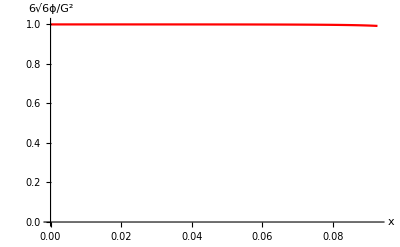

```mathematica
Show[Table[Plot[(6 √6 sols[[i]][[1]][(x-1+1)/q])/(sols[[i]][[2]][(x-1+1)/q])^2//Evaluate,{x,1+q ϵ-1,1+q results[[;;,;;,2]][[1,i]]-1},PlotStyle->plotStyles[[i]],PlotLegends->plotLegends[[i]],AxesLabel->{Style["x",16],Style["6√6ϕ/G^2",16]},WorkingPrecision->100,PlotPoints->100],{i,Length[sols]}],PlotRange->{0,1.01},AxesOrigin->{0,0}]
```

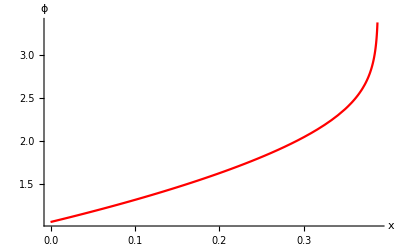

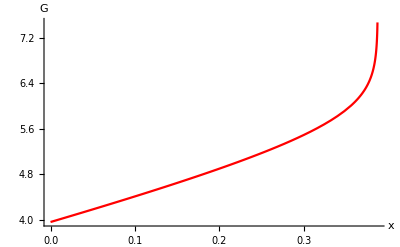

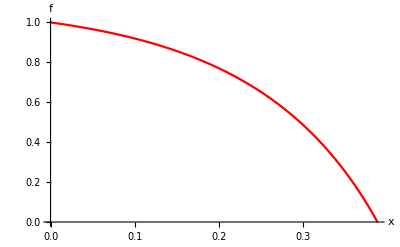

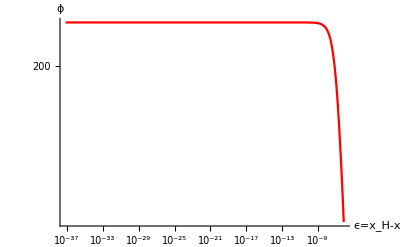

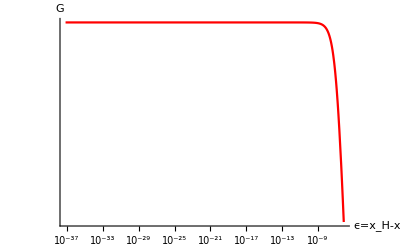

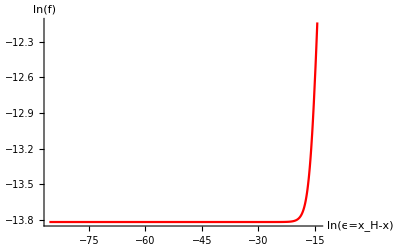

```mathematica
plotStyles=Table[Hue[Rescale[i,{1,Length[sols]}]],{i,Length[sols]}];
plotLegends=Table[StringForm["q/k=``",results[[;;,;;,1]][[1,i]]],{i,Length[sols]}];
Show[Table[Plot[sols[[i]][[1]][(x-1+1)/q]//Evaluate,{x,1+q ϵ-1,1+q results[[;;,;;,2]][[1,i]]-1},PlotStyle->plotStyles[[i]],PlotLegends->plotLegends[[i]],AxesLabel->{Style["x",16],Style["ϕ",16]}],{i,Length[sols]}],PlotRange->All]
Show[Table[Plot[sols[[i]][[2]][(x-1+1)/q]//Evaluate,{x,1+q ϵ-1,1+q results[[;;,;;,2]][[1,i]]-1},PlotStyle->plotStyles[[i]],PlotLegends->plotLegends[[i]],AxesLabel->{Style["x",16],Style["G",16]}],{i,Length[sols]}],PlotRange->All]
Show[Table[Plot[sols[[i]][[3]][(x-1+1)/q]//Evaluate,{x,1+q ϵ-1,1+q results[[;;,;;,2]][[1,i]]-1},PlotStyle->plotStyles[[i]],PlotLegends->plotLegends[[i]],AxesLabel->{Style["x",16],Style["f",16]}],{i,Length[sols]}],PlotRange->All]
Show[Table[LogLogPlot[sols[[i]][[1]][results[[;;,;;,2]][[1,i]]-(x-1+1)/q]//Evaluate,{x,1+q ϵ-1,1+q results[[;;,;;,2]][[1,i]]-1},PlotStyle->plotStyles[[i]],PlotLegends->plotLegends[[i]],AxesLabel->{Style["ϵ=x_H-x",16],Style["ϕ",16]},WorkingPrecision->100],{i,Length[sols]}],PlotRange->All]
Show[Table[LogLogPlot[sols[[i]][[2]][results[[;;,;;,2]][[1,i]]-(x-1+1)/q]//Evaluate,{x,1+q ϵ-1,1+q results[[;;,;;,2]][[1,i]]-1},PlotStyle->plotStyles[[i]],PlotLegends->plotLegends[[i]],AxesLabel->{Style["ϵ=x_H-x",16],Style["G",16]},WorkingPrecision->100],{i,Length[sols]}],PlotRange->All]
Show[Table[Plot[Log[sols[[i]][[3]][results[[;;,;;,2]][[1,i]]-(E^lnx-1+1)/q]]//Evaluate,{lnx,Log[1+q ϵ-1],Log[1+q results[[;;,;;,2]][[1,i]]-1]},PlotStyle->plotStyles[[i]],PlotLegends->plotLegends[[i]],AxesLabel->{Style["ln(ϵ=x_H-x)",16],Style["ln(f)",16]},WorkingPrecision->100],{i,Length[sols]}],PlotRange->All]
```